```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
```

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
LEC={
{0.50,5.182,-16.3721,4.4445},
{1.00,4.215,-44.4515,27.245},
{2.00,3.594,-142.3765,173.925},
{3.00,3.378,-295.93,566.65},
{4.00,3.270,-505.15,1426.75},
{6.00,3.164,-1090.548,6552.5},
{8.00,3.111,-1898.553,25697},
{10.0,3.075,-2929.165,92495}};
a11Rimas={-137.45,-45.726,-25.651,-20.496,-18.184,-16.026,-14.863,-13.457};
(* Universal a2>10^5 E3=0.01 ℏ=m=c=1*)
uLEC={
{1.00,1,-0.671,0.678},
{2.00,1,-2.684,7.749},
{3.00,1,-10.736,194.253},
{4.00,1,-24.156,4273.294},
{6.00,1,-42.944,122391.358},
{10.0,1,-67.100,4102409.239}};
activeLEC=LEC;
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for DIMER-DIMER (AB-AB)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
Vc[r_,lam_,Cc_]:=Cc Exp[-lam r^2];

VlocDD[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta,w},
eta=2 Cc (2 Aa/(2 Aa+lam))^(3/2);
w=(2 Aa lam/(2 Aa+lam));
 eta Exp[-w r^2]
];

WnolocDD[r_,rp_,e_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,a1,b1,c1,a2,b2,c2},
zeta1=8 Aa^(3/2) 1/TwoMyOverHBsq;
zeta2=-16 Aa^(3/2) Cc (2 Aa/(2 Aa+lam))^(3/2);
a1=Aa;c1=a1;
a2=Aa (2 Aa+3 lam)/(2 Aa+lam);
c2=Aa;
-(4 Pi r rp) (
 zeta1 Exp[-a1 r^2-c1 rp^2] (-(4 (a1)^2 r^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq e) I^Ll KroneckerDelta[Ll,0]
+I^Ll zeta2 KroneckerDelta[Ll,0] Exp[-a2 r^2-c2 rp^2]
)
];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for DIMER-FERMION (AB-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
VlocDF[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta,w},
eta=8 Cc (Aa/(4 Aa+lam))^(3/2);
w=4 Aa lam/(4 Aa+lam);
eta Exp[-w r^2]
];

WnolocDF[r_,rp_,e_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,a1,b1,c1,a2,b2,c2},
zeta1=(64/27) (2 Aa)^(3/2) 1/TwoMyOverHBsq;
zeta2=-(64/27) (2 Aa)^(3/2) Cc;
a1=(10/9) Aa;c1=a1;
b1=(16/9) Aa;
a2=(2/9) (5 Aa+8 lam);c2=(2/9) (5 Aa+2 lam);
b2=(16/9) (Aa+lam);
-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 (a1)^2 r^2+(b1)^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq e) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}]
)
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
)];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
VlocTF[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta2,eta3,w2,w3},
eta2=2 Cc (3 Aa/(3 Aa+lam))^(3/2);
w2=3 Aa lam/(3 Aa+lam);
eta3=8 Dd (3 Aa^2/(12 Aa^2+16 Aa lam+lam^2))^(3/2);
w3=(12 Aa lam (Aa+lam)/(12 Aa^2+16 Aa lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27/8)(3/2 Aa)^(3/2) (1./TwoMyOverHBsq);
a1=(Aa 15/16);
b1=(Aa 18/16);
c1=a1;

zeta2=-2 27 (Aa 3/2)^(3./2) Cc (Aa/(4 Aa+lam))^(3/2);
zeta3=-27 (Aa 3/2)^(3./2) Dd (Aa/(4 Aa+5 lam))^(3/2);

a2=3 Aa (5 Aa+8 lam)/(4 (4 Aa+lam));
b2=9 Aa (Aa+lam)/(2 (4 Aa+lam));
c2=3 Aa (5 Aa+2 lam)/(4 (4 Aa+lam));

a3=3 (20 Aa^2+52 Aa lam+27 lam^2)/(4 (16 Aa+20 lam));
b3=9 (4 Aa^2+8 Aa lam+3 lam^2)/(2 (16 Aa+20 lam));
c3=3 (20 Aa^2+28 Aa lam+3 lam^2)/(4 (16 Aa+20 lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV],

```mathematica
SolveLocal[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq Vc[i hDif,lam,c0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

Amat=Dmat+Kmat;

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a0_?NumberQ,cfg0_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Switch[cfg0
,{3,1},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
,{2,1},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocDF[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocDF[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];
,{2,2},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocDD[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocDD[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];
];

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

Amat=Dmat+Kmat+Wmat;

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=150;
cfg={3,1};
k0FM=0.01;
Switch[cfg[[1]],
1,afit=4.5;rr=10.0,
2,afit=6.0;rr=25.0,
3,afit=3.1;rr=25.0; 
];
hbar=197.327053;
Mm=938.92;
m1=cfg[[1]] Mm;m2=cfg[[2]] Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV

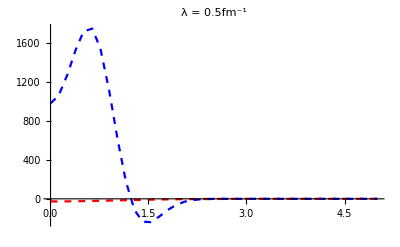

-Graphics3D-

```mathematica
nn=1;
energ=(k0FM hbar)^2/(2 μ);
rp=1.1;
Lrel=1;
Plot[
{VlocTF[R,activeLEC[[nn]][[1]],activeLEC[[nn]][[3]],activeLEC[[nn]][[4]],afit],Re[WnolocTF[R,rp,energ,activeLEC[[nn]][[1]],activeLEC[[nn]][[3]],activeLEC[[nn]][[4]],afit,Lrel,mh2]]},{R,0.01,5.0},PlotPoints->40,MaxRecursion->0,PlotLegends->{MaTeX["V_\\text{local}",Magnification->1.6],MaTeX["V_\\text{non-local}",Magnification->1.6]},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},AxesLabel->{MaTeX["R~[\\text{fm}]",Magnification->1.6]},PlotLabel->"λ = "<>ToString[activeLEC[[nn]][[1]]]<>"fm^-1",PlotRange->Full]

Plot3D[Re[WnolocTF[rr,rp,0.0001,activeLEC[[nn]][[1]],activeLEC[[nn]][[3]],activeLEC[[nn]][[4]],0.6,Lrel,mh2]],{rr,0.01,4.0},{rp,0.01,4.0},PlotRange->Full]
```

S-wave scattering length -- used to calibrate α

we chose the singlet value a_s≈4±1fm (3-1) and a_s≈6±0.2fm (2-1) to ensure calibrate the α core parameter of the triton and deuteron;
(cf. https://arxiv.org/pdf/1105.3763.pdf )

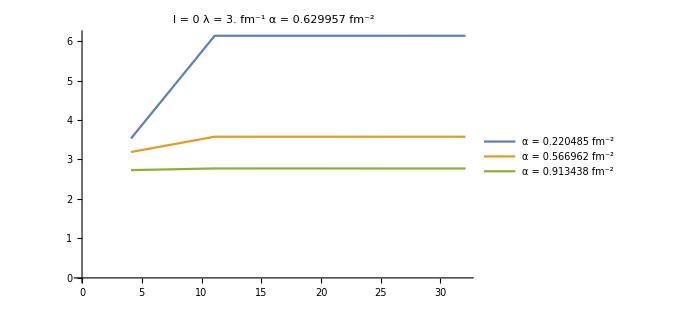

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];
Lrel=0;
k0FM=0.1;
nGrid=250;
aOfa={};
rRange=Subdivide[4.1,32.1,4];
nn=Min[4,Length[activeLEC]];
afit=αL[[nn]][[2]];
αRange=Subdivide[0.35 afit,1.45 afit,2];

Do[
aS={};
SetSharedVariable[aS];
ParallelDo[

λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];
TanDelSwave=Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aS,{rr,-TanDelSwave/k0FM^(2 Lrel+1)}];

,{rr,rRange}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
AppendTo[aOfa,a0];
,{α0,αRange}];
leg="α = "<>ToString[#]<>" fm^-2"&/@αRange;
ListPlot[aOfa,AxesLabel->{MaTeX["R_\\text{max}~\\left[\\text{fm}\\right]",Magnification->1.6],MaTeX["a~\\left[\\text{fm}^{2l+1}\\right]",Magnification->1.6]},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,Joined->True,PlotLabel->Style["l = "<>ToString[Lrel]<>"  λ = "<>ToString[activeLEC⟦nn⟧[[1]]]<>" fm^-1"<>"  α = "<>ToString[αL⟦nn⟧[[2]]]<>" fm^-2",Orange,16]]
```

α-fitting

```mathematica
doSwaveFit=0;
If[doSwaveFit==1,
rr=20;
nGrid=200;
k0FM=0.1;
αL={};
Lrel=0;
SetSharedVariable[αL];

ParallelDo[
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];
afit=activeLEC⟦nn⟧[[2]];
aini=(10./2.) afit^(-2);
alfL=FindRoot[Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,alf,cfg,mh2]]==(-k0FM afit),{alf,aini},PrecisionGoal->4];
Print["λ = ",λ," : ",Chop[alf/.alfL]];
AppendTo[αL,{λ,alf/.Chop[alfL]}];
,{nn,λRange}];
αL=Sort[αL];
Put[αL,LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]]]
```

```mathematica
(*αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];*)
αL=Import[NotebookDirectory[]<>"../data/RGM_alpha_Fit2Martin.dat","Table"];
a00Rimas=Transpose[{0.25 activeLEC[[λRange]][[All,1]]^2,activeLEC[[λRange]][[All,2]]}];
a1Rimas=Transpose[{0.25 activeLEC[[λRange]][[All,1]]^2,a11Rimas[[λRange]]}];
αScale={1.};(*Subdivide[0.1,1,20];*)
k0FM=0.1;nGrid=200;
aS={};aP={};
SetSharedVariable[aS,aP];
Do[
ParallelDo[
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];
α0=na Select[αL,#[[1]]==λ&][[1]][[2]];
TanDel=Chop[SolveSecular[rr,nGrid,k0FM,0,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aS,{λ,na,-TanDel/k0FM}];
TanDel=Chop[SolveSecular[rr,nGrid,k0FM,1,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aP,{λ,na,-TanDel/k0FM^3}];
,{nn,λRange}];
,{na,αScale}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
a1=Reverse[Sort[aP,#1[[1]]>#2[[1]]&]];
```

Part::partw: Part 1 of {} does not exist.

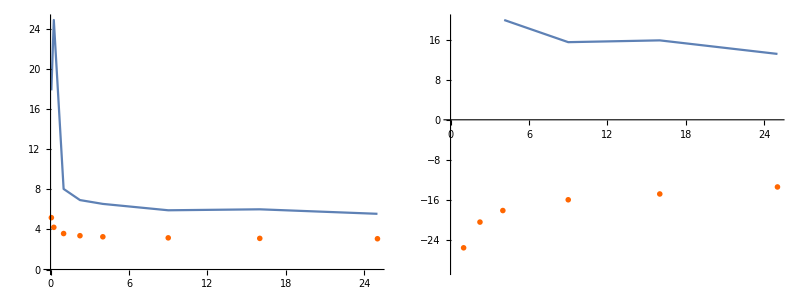

```mathematica
a0Plot=Table[Transpose[{0.25 activeLEC[[λRange]][[All,1]]^2,Select[a0,#[[2]]==αScale[[anPlot]]&][[All,3]]}],{anPlot,1,Length[αScale]}];
a1Plot=Table[Transpose[{0.25 activeLEC[[λRange]][[All,1]]^2,Select[a1,#[[2]]==αScale[[anPlot]]&][[All,3]]}],{anPlot,1,Length[αScale]}];
Grid[{{
Show[ListPlot[a0Plot,AxesLabel->{MaTeX["\\lambda \\left[\\text{fm}^{-1}\\right]",Magnification->2],MaTeX["a_\\text{S-wave} \\left[\\text{fm}\\right]",Magnification->2]},ImageSize->500,PlotRange->Automatic,Joined->True],ListPlot[a00Rimas,PlotTheme->"Marketing",AspectRatio->1]],
Show[ListPlot[a1Plot,AxesLabel->{MaTeX["\\lambda \\left[\\text{fm}^{-1}\\right]",Magnification->2],MaTeX["a_\\text{P-wave} \\left[\\text{fm}^3\\right]",Magnification->2]},ImageSize->500,PlotRange->{Automatic,{-30,20}},Joined->True],ListPlot[a1Rimas,PlotTheme->"Marketing",AspectRatio->1]]
}}]
```

```mathematica
-a1[[All,3]] k0FM^3
```

{-0.435677,-0.14753,-0.0328772,-0.0232906,-0.0200936,-0.0155561,-0.0159167,-0.013201}

```mathematica
Export[NotebookDirectory[]<>"../data/RGM_a0.dat",a0,"Table"]
Export[NotebookDirectory[]<>"../data/RGM_a1.dat",a1,"Table"]
Export[NotebookDirectory[]<>"../data/RGM_alpha.dat",αL,"Table"]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica/../data/RGM_a0.dat

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica/../data/RGM_a1.dat

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica/../data/RGM_alpha.dat

S- and P-wave phase shifts

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];
αL=Import[NotebookDirectory[]<>"../data/RGM_alpha_Fit2Martin.dat","Table"];

rr=20;
nn=Length[activeLEC];

tanDsL={};tanDpL={};

Do[
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];
α0=Select[αL,#[[1]]==λ&][[1]][[2]];
k0FM=0.06;
ErangeMeV=Subdivide[(k0FM hbar)^2/(2 μ),2.0,20];

nGrid=200;

tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];
ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,α0,cfg,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,α0,cfg,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];
tnDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]];
tnDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]];
AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];
,{nn,λRange}]
```

Part::partw: Part 1 of {} does not exist.

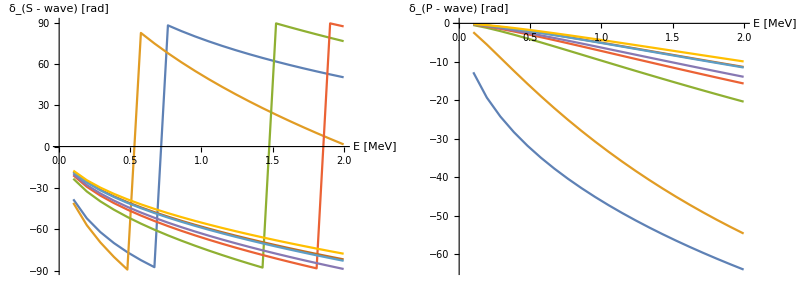

```mathematica
phaseS=Table[Transpose[{tanDsL[[nn]][[All,1]],180./Pi ArcTan[tanDsL[[nn]][[All,2]]]}],{nn,λRange}];
phaseP=Table[Transpose[{tanDpL[[nn]][[All,1]],180./Pi ArcTan[tanDpL[[nn]][[All,2]]]}],{nn,λRange}];
(*leg="α = "<>ToString[α0]<>" fm^-2    L_rel = "<>ToString[#]&/@{0,1};*)
Grid[{{ListPlot[phaseS,AxesLabel->{"E [MeV]","δ_(S - wave) [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True],
ListPlot[phaseP,AxesLabel->{"E [MeV]","δ_(P - wave) [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True]}}]
```

```mathematica
Lrel = 0;
dataS=Table[Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/tanDsL[[nn]][[All,2]]}],{nn,λRange}];
EreS=Table[Fit[dataS[[nn]][[;;]],{1,p^2},p],{nn,λRange}];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Table[Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDpL[[nn]][[All,2]]}],{nn,λRange}];;
EreP=Table[Fit[dataP[[nn]][[;;]],{1,p^2},p],{nn,λRange}];;
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
Do[
λ=0.25 activeLEC⟦nn⟧[[1]]^2;
Print["λ = ",λ,"  :  a_s = ",a0tf[[nn]]," fm    r_s = ",r0tf[[nn]]," fm        a_p = ",a1tf[[nn]]," fm^3     r_p = ",r1tf[[nn]]," fm"];
,{nn,λRange}];
```

λ = 0.0625  :  a_s = 9.37631 fm    r_s = 8.61109 fm        a_p = 657.172 fm^3     r_p = -0.249552 fm

λ = 0.25  :  a_s = 0.746203 fm    r_s = 115.371 fm        a_p = 166.581 fm^3     r_p = -0.244895 fm

λ = 1.  :  a_s = 6.34388 fm    r_s = 5.88703 fm        a_p = 36.933 fm^3     r_p = -0.717962 fm

λ = 2.25  :  a_s = 5.8364 fm    r_s = 4.94152 fm        a_p = 25.762 fm^3     r_p = -0.863157 fm

λ = 4.  :  a_s = 5.62438 fm    r_s = 4.62897 fm        a_p = 22.0966 fm^3     r_p = -0.936181 fm

λ = 9.  :  a_s = 5.23242 fm    r_s = 4.12385 fm        a_p = 16.916 fm^3     r_p = -1.06045 fm

λ = 16.  :  a_s = 5.29662 fm    r_s = 4.19055 fm        a_p = 17.3583 fm^3     r_p = -1.06759 fm

λ = 25.  :  a_s = 4.99714 fm    r_s = 3.83942 fm        a_p = 14.2708 fm^3     r_p = -1.15649 fm

(-0.0608585-0.682138 ⅈ | -0.0608585+0.682138 ⅈ
0.638135-0.0729328 ⅈ | 0.638135+0.0729328 ⅈ
-0.114899-1.47612 ⅈ | -0.114899+1.47612 ⅈ
-0.347204-1.88555 ⅈ | -0.347204+1.88555 ⅈ
-0.456712-2.07417 ⅈ | -0.456712+2.07417 ⅈ
-0.688871-2.46825 ⅈ | -0.688871+2.46825 ⅈ
-0.657543-2.40288 ⅈ | -0.657543+2.40288 ⅈ
-0.869027-2.74787 ⅈ | -0.869027+2.74787 ⅈ)

(-0.115015-0.480554 ⅈ | -0.200414+0. ⅈ | -0.115015+0.480554 ⅈ
0.0987025-1.11121 ⅈ | -0.611933+0. ⅈ | 0.0987025+1.11121 ⅈ
-1.13141-3.2615 ⅈ | -1.30002+0. ⅈ | -1.13141+3.2615 ⅈ
-1.77621-4.09655 ⅈ | -1.59716+0. ⅈ | -1.77621+4.09655 ⅈ
-2.15876-4.49567 ⅈ | -1.74025+0. ⅈ | -2.15876+4.49567 ⅈ
-2.86714-5.29231 ⅈ | -2.0385+0. ⅈ | -2.86714+5.29231 ⅈ
-2.94568-5.16062 ⅈ | -1.98637+0. ⅈ | -2.94568+5.16062 ⅈ
-3.49995-5.82953 ⅈ | -2.24444+0. ⅈ | -3.49995+5.82953 ⅈ)

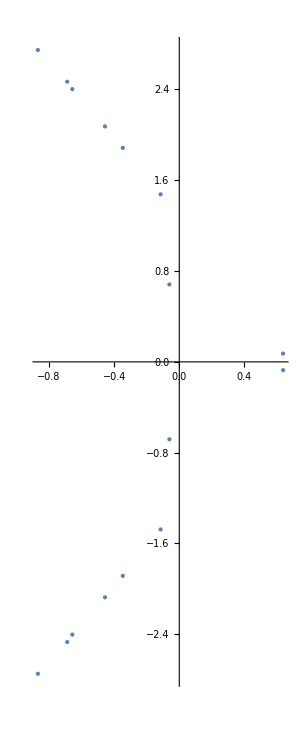
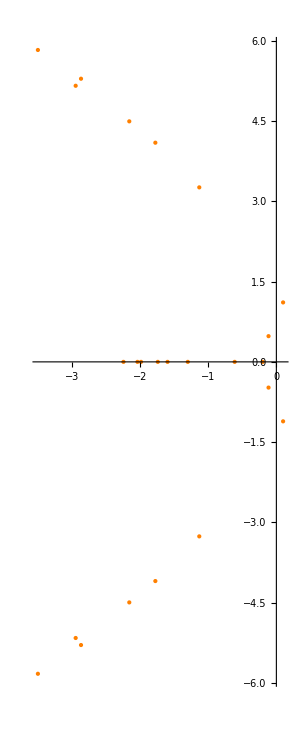
-Graphics- | -Graphics-

```mathematica
ascale=1.;
rscale=1.;
a0tf=ascale a0tf;r0tf=rscale r0tf;a1tf=ascale a1tf;r1tf=rscale r1tf;

Spoles=Table[Solve[-1/a0tf[[nn]]+0.5 r0tf[[nn]] k^2-I k==0,k],{nn,λRange}];
SPoleTable=hbar^2/(2 μ) ((k/.Spoles)^2);

PPoles=Table[Solve[-1/a1tf[[nn]]+0.5 r1tf[[nn]] k^2-I k^3==0,k],{nn,λRange}];
PPoleTable=hbar^2/(2 μ) ((k/.PPoles)^2);
SPoleTable//MatrixForm
PPoleTable//MatrixForm
Grid[{{
ComplexListPlot[Flatten[SPoleTable],AxesLabel->{MaTeX["\\text{Im}\\left(E\\right) \\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\text{Re}\\left(E\\right) \\left[\\text{MeV}\\right]",Magnification->2]},ImageSize->300,PlotLegends->{MaTeX["-\\frac{1}{a_\\text{S-wave}}+\\frac{r_\\text{S-wave}}{2}k^2-ik=0",Magnification->1.5]},PlotStyle->PointSize[Large],PlotRange->Automatic],
ComplexListPlot[Flatten[PPoleTable],AxesLabel->{MaTeX["\\text{Im}\\left(E\\right) \\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\text{Re}\\left(E\\right) \\left[\\text{MeV}\\right]",Magnification->2]},ImageSize->300,PlotLegends->{MaTeX["-\\frac{1}{a_\\text{P-wave}}+\\frac{r_\\text{P-wave}}{2}k^2-ik^3=0",Magnification->1.5]},PlotStyle->{Orange,PointSize[Large]},PlotRange->Automatic]
}}]
```

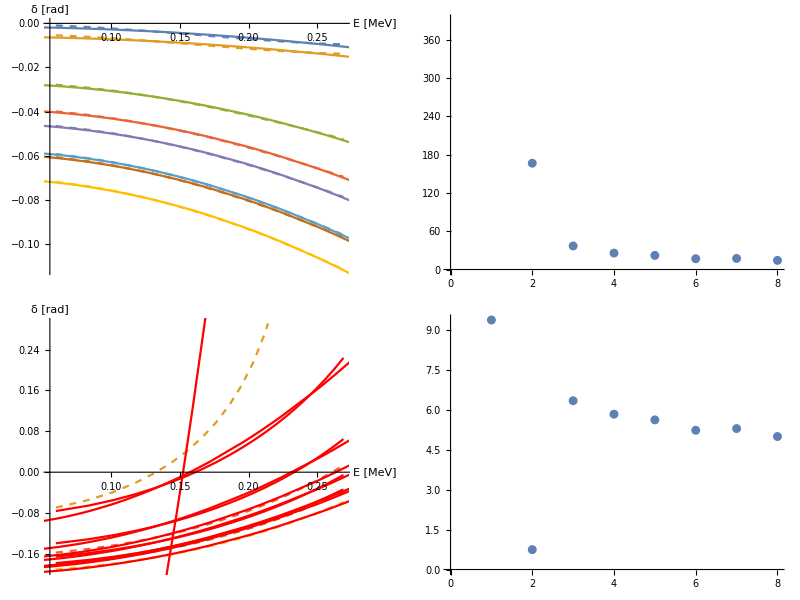

```mathematica
Grid[{{
Show[
ListPlot[dataP,AxesLabel->{"E [MeV]","δ [rad]"},ImageSize->500,PlotRange->Automatic,Joined->True,PlotStyle->Dashed],Plot[EreP,{p,0,10}]
],ListPlot[a1tf,ImageSize->500]
},{
Show[
ListPlot[dataS,AxesLabel->{"E [MeV]","δ [rad]"},ImageSize->500,PlotRange->Automatic,Joined->True,PlotStyle->{Red,Dashed}],Plot[EreS,{p,0,10},PlotStyle->Red]
],ListPlot[a0tf,ImageSize->500]
}}]
```

S-matrix pole (S-wave)

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];

Lrel=0;

data={};
Do[
Xl={};
SetSharedVariable[Xl];
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];α0=Select[αL,#[[1]]==λ&][[1]][[2]];

Print["λ="<>ToString[λ]<>"fm^-2  ;   α="<>ToString[α0]<>"fm^-2"];

ParallelDo[
momFM=Sqrt[2 μ En/hbar^2];
TanDel=Chop[SolveSecular[rr,nGrid,momFM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[Xl,{En,((2 μ En)^(Lrel+0.5))/TanDel}];
,{En,ErangeMeV}];

Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,{λ,Xlr}];

,{nn,λRange}]
Put[data,LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]
```

λ=0.0625fm^-2  ;   α=0.217329fm^-2

λ=0.25fm^-2  ;   α=0.411572fm^-2

λ=1.fm^-2  ;   α=0.560964fm^-2

λ=2.25fm^-2  ;   α=0.629957fm^-2

λ=4.fm^-2  ;   α=0.669035fm^-2

λ=9.fm^-2  ;   α=0.710376fm^-2

λ=16.fm^-2  ;   α=0.731732fm^-2

λ=25.fm^-2  ;   α=0.746071fm^-2

LocalObject[file:///home/kirscher/.Wolfram/Objects/Swave_3-1_TanDelta]

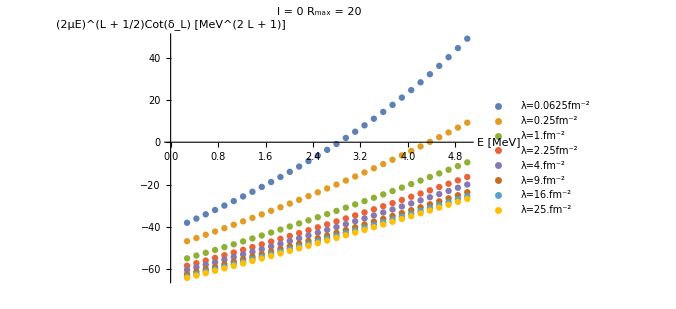

```mathematica
data=Get[LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]];
legs="λ="<>ToString[#[[1]]]<>"fm^-2"&/@data;
ListPlot[data[[All,2]],AxesLabel->{"E [MeV]","(2μE)^(L + 1/2)Cot(δ_L) [MeV^(2  L + 1)]"},ImageSize->500,PlotLegends->legs,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel]<>"   R_max = "<>ToString[rr],Orange,16]]
```

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k^2)=(P_N^(l)(k^2))/(Q_M^(l)(k^2))=(p_0+p_1 z+p_2 z^2+p_3 z^3+…)/(1+q_1 z+q_2 z^2+q_3 z^3+…):=k^(2l+1)cotδ_l=-1/a_l+1/2 r_l k^2-1/4 P_l k^4+…  

⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

LocalObject::nso: LocalObject[file:///home/kirscher/.Wolfram/Objects/ErangeMeVS] not found.

-Graphics-

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

Plot::plln: Limiting value $Failed⟦1⟧ in {ee,$Failed⟦1⟧,$Failed⟦-1⟧} is not a machine-sized real number.

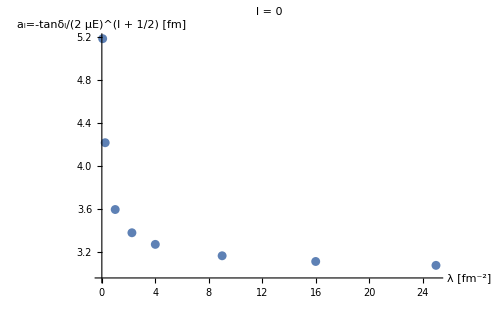
Plot[(modelX/.#1⟦2⟧/.ee→em&)/@PadeSolus,{ee,ErangeMeV⟦1⟧,ErangeMeV⟦-1⟧},AxesLabel→{E [MeV],(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]},ImageSize→500,PlotRange→Automatic,PlotLabel→Style[l = <>ToString[Lrel],Orange,16],Epilog→Point/@(#1⟦2⟧&)/@data] | -Graphics-

```mathematica
data=Get[LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]];
ErangeMeV=Get[LocalObject["ErangeMeVS"]];
Poles={};PadeSolus={};Lrel=0;

PadeOrderN=3;PadeOrderM=1;

Do[
Clear[coffs];
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-0.01,1.2},Length[Flatten[coffs]]]}];
constr=10^1>#>-10^1&/@Flatten[coffs];
Union[constr,{}];

PadePolyP=coffs[[1]][[PadeOrderN+1]]+Sum[coffs[[1]][[i]] ee^i,{i,1,PadeOrderN}];
PadePolyQ=1+Sum[coffs[[2]][[i]] ee^i,{i,1,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

efitmax=Position[Table[If[data[[n]][[2]][[nn]][[2]]<data[[n]][[2]][[nn+1]][[2]],data[[n]][[2]][[nn]],"42"],{nn,Range[Length[data[[n]][[2]]]-1]}],"42"];
If[efitmax=={},efitmax=Length[data[[n]][[2]]],efitmax=Flatten[efitmax][[1]]];
fitdata=data[[n]][[2]][[;;efitmax]];

solu=FindFit[fitdata,{modelX,constr},Flatten[coffs],ee,MaxIterations->500];

poles=Solve[((PadePolyP/PadePolyQ-I (2 μ ee)^(Lrel+0.5))/.solu)==0,ee];

(*Print["λ = ",data[[n]][[1]],"   : E_pole = ",poles];(*,"   ",solu];*)*)
AppendTo[Poles,Transpose[{Table[data[[n]][[1]],Length[poles]],Flatten[ee/.poles]}]];
AppendTo[PadeSolus,{data[[n]][[1]],solu}];
,{n,Range[Length[data]]}]
tmp=Transpose[{#[[1]]&/@Flatten[Poles,1],Re[#[[2]]]&/@Flatten[Poles,1],Im[#[[2]]]&/@Flatten[Poles,1]}];
Export[NotebookDirectory[]<>"pole_data_Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>".dat",tmp,"Table","FieldSeparators"->"    "];
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Re[Poland];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"Re[E_res] [MeV]","Im[E_res] [MeV]"},ImageSize->500]}}]
Grid[{{Plot[(modelX/.#[[2]]/.ee->em)&/@PadeSolus,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-tanδ_l/(2  μE)^(l + 1/2) [fm]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

P-wave

here we assess the convergence of the integration with box size (rr)
ECCE: for d-d, the non-local potential is zero in accordance with the symmetric exchange of the bose particle (AB); the remaining
             local interaction goes to zero for  λ → ∞; therefore, the free solution exhibits a strong box-size dependence

```mathematica
nGrid=200;
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];
Lrel=1;
aL={};
aPwfkt={};
SetSharedVariable[aL];
k0FM=0.001;
rr=20;

ParallelDo[
λ=0.25 activeLEC⟦mm⟧[[1]]^2;C0=activeLEC⟦mm⟧[[3]];D0=activeLEC⟦mm⟧[[4]];α0=Select[αL,#[[1]]==λ&][[1]][[2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aL,{λ,-TanDelPwave/k0FM^(2 Lrel+1)}];
,{mm,Range[Length[activeLEC]]}];

a1=Reverse[Sort[aL,#1[[1]]>#2[[1]]&]];

leg="α = "<>ToString[α0]<>" fm^-2";
ListPlot[{a0,a1},AxesLabel->{"λ [fm^-1]","-k^(2  l + 1)·tan(δ_k_0) [fm^3]"},ImageSize->500,PlotLegends->{"a_S","a_P"},PlotRange->{Automatic,Automatic},PlotLabel->Style["l = "<>ToString[Lrel]<>"   k_0 = "<>ToString[k0FM]<>"  fm^-1",Orange,16]]
```

ListPlot::lpn: {{},{{0.0625,-22.1269},{0.25,8.15487},{1.,5.41576},{2.25,4.31298},{4.,3.80229},{9.,3.32809},{16.,3.10138},{25.,2.95825}}} is not a list of numbers or pairs of numbers.

ListPlot[{{{0.0625,1.,17.9025},{0.25,1.,24.9343},{1.,1.,8.05077},{2.25,1.,6.93915},{4.,1.,6.55576},{9.,1.,5.91872},{16.,1.,6.0153},{25.,1.,5.56595}},{{0.0625,-22.1269},{0.25,8.15487},{1.,5.41576},{2.25,4.31298},{4.,3.80229},{9.,3.32809},{16.,3.10138},{25.,2.95825}}},AxesLabel→{λ [fm^-1],-k^(2  l + 1)·tan(δ_k_0) [fm^3]},ImageSize→500,PlotLegends→{a_S,a_P},PlotRange→{Automatic,Automatic},PlotLabel→l = 1   k_0 = 0.001  fm^-1]

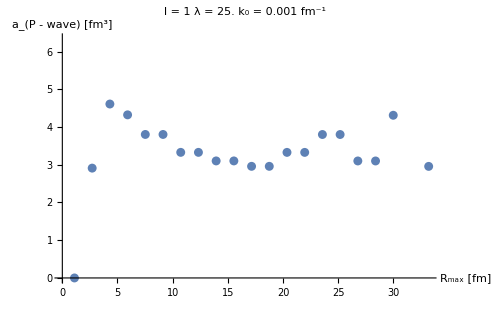

```mathematica
nGrid=200;
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];
Lrel=1;
rRange=Subdivide[1.1,33.2,20];
aP={};
aPwfkt={};
SetSharedVariable[aP];
k0FM=0.001;
nn=Length[activeLEC];
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];α0=Select[αL,#[[1]]==λ&][[1]][[2]];

ParallelDo[
TanDelPwave=Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aP,{rr,-TanDelPwave/k0FM^(2 Lrel+1)}];
,{rr,rRange}];

a1=Reverse[Sort[aP,#1[[1]]>#2[[1]]&]];

leg="α = "<>ToString[α0]<>" fm^-2";
ListPlot[a1,AxesLabel->{"R_max [fm]","a_(P - wave) [fm^3]"},ImageSize->500,PlotLegends->leg,PlotRange->{Automatic,Automatic},PlotLabel->Style["l = "<>ToString[Lrel]<>"   λ = "<>ToString[λ]<>"   k_0 = "<>ToString[k0FM]<>"  fm^-1",Orange,16]]
```

S-matrix pole (P-wave)

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_CorePara"]];
nGrid=200;
ErangeMeV=Range[(k0FM hbar)^2/(2 μ),25.0,1];
Put[ErangeMeV,LocalObject["ErangeMeVP"]];
rr=20;
Lrel=1;

data={};
Do[
Xl={};
SetSharedVariable[Xl];
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[3]];D0=activeLEC⟦nn⟧[[4]];
α0=Select[αL,#[[1]]==λ&][[1]][[2]];
Print["λ="<>ToString[λ]<>"fm^-2  ;   α="<>ToString[α0]<>"fm^-2"];

ParallelDo[
momFM=(2 μ En/hbar^2)^0.5;
TanDel=Chop[SolveSecular[rr,nGrid,momFM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[Xl,{momFM,(momFM^(2 Lrel+1))/TanDel}];
,{En,ErangeMeV}];

Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,{λ,Xlr}];
,{nn,λRange}]
Put[data,LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]
```

λ=0.0625fm^-2  ;   α=0.217329fm^-2

λ=0.25fm^-2  ;   α=0.411572fm^-2

λ=1.fm^-2  ;   α=0.560964fm^-2

λ=2.25fm^-2  ;   α=0.629957fm^-2

$Aborted

LocalObject[file:///home/kirscher/.Wolfram/Objects/Pwave_3-1_TanDelta]

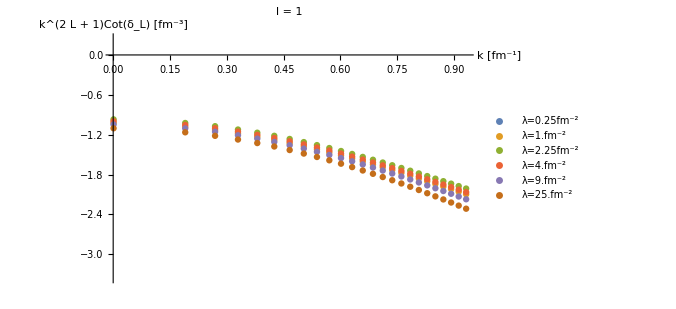

```mathematica
data=Re[Get[LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]];
legs="λ="<>ToString[#[[1]]]<>"fm^-2"&/@data;
ListPlot[data[[All,2]],AxesLabel->{"k [fm^-1]","k^(2  L + 1)Cot(δ_L) [fm^-3]"},ImageSize->500,PlotLegends->legs,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k)=(P_N^(l)(k^2))/(Q_M^(l)(k^2)):=k^(2l+1)cotδ_l  ⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

FindFit::sdir: Search direction has become too small.

-Graphics-

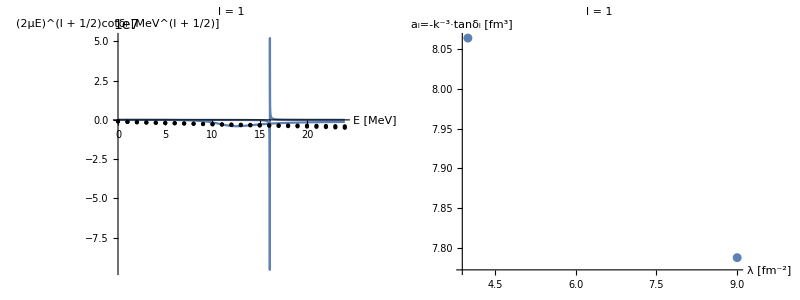

```mathematica
data=Re[Get[LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]];
ErangeMeV=Get[LocalObject["ErangeMeVP"]];

Poles={};PadeSolus={};Lrel=1;

PadeOrderN=3;PadeOrderM=2;

Do[
Clear[coffs];
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-0.01,0.2},Length[Flatten[coffs]]]}];
constr=10^2>#>-10^2&/@Flatten[coffs];
Union[constr,{}];

PadePolyP=coffs[[1]][[PadeOrderN+1]]+Sum[coffs[[1]][[i]] ee^i,{i,1,PadeOrderN}];
PadePolyQ=1+Sum[coffs[[2]][[i]] ee^i,{i,1,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

dati=data[[n]][[2]][[All,2]];
(*efitmax=Position[Table[If[data[[n]][[2]][[nn]][[2]]<data[[n]][[2]][[nn+1]][[2]],data[[n]][[2]][[nn]],"42"],{nn,Range[Length[data[[n]][[2]]]-1]}],"42"];*)
efitmax=Position[Differences[dati,1],Max[Differences[dati,1]]][[1]][[1]];
If[efitmax=={},efitmax=Length[data[[n]][[2]]],efitmax=Flatten[efitmax][[1]]];
fitdata=data[[n]][[2]][[;;efitmax]];

solu=FindFit[fitdata,{modelX,constr},Flatten[coffs],ee,MaxIterations->500];

poles=Solve[((modelX-I (2 μ ee)^(Lrel+0.5))/.solu)==0,ee];

(*Print["λ = ",data[[n]][[1]],"   : E_pole = ",poles];(*,"   ",solu];*)*)
AppendTo[Poles,Transpose[{Table[data[[n]][[1]],Length[poles]],Flatten[ee/.poles]}]];
AppendTo[PadeSolus,{data[[n]][[1]],solu}];
,{n,Range[Length[data]]}]

tmp=Transpose[{#[[1]]&/@Flatten[Poles,1],Re[#[[2]]]&/@Flatten[Poles,1],Im[#[[2]]]&/@Flatten[Poles,1]}];
Export[NotebookDirectory[]<>"pole_data_Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>".dat",tmp,"Table","FieldSeparators"->"    "];
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Re[Poland];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->Full,AxesLabel->{"Re[E_res] [MeV]","Im[E_res] [MeV]"},ImageSize->500]}}]
Grid[{{Plot[(modelX/.#[[2]]/.ee->em)&/@PadeSolus,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar^(2 Lrel+1)/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-k^-3·tanδ_l [fm^3]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

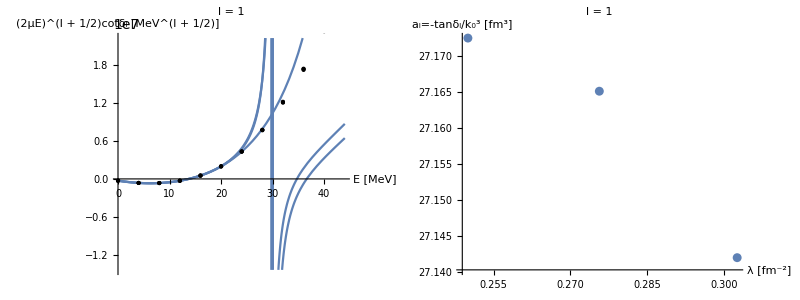

```mathematica
Grid[{{Plot[(#[[2]][[-1]]/.ee->em)&/@SoleSet,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar^(2 Lrel+1)/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-tanδ_l/k_0^3 [fm^3]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

S-wave scattering length limit cycle

assume C_nn∝λ^2 and set D_nnn=0

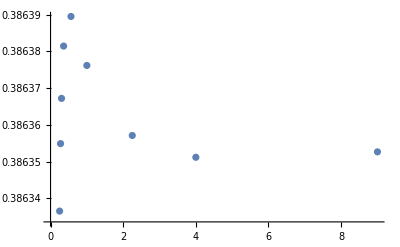

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_CorePara"]];
ListPlot[αL]
```

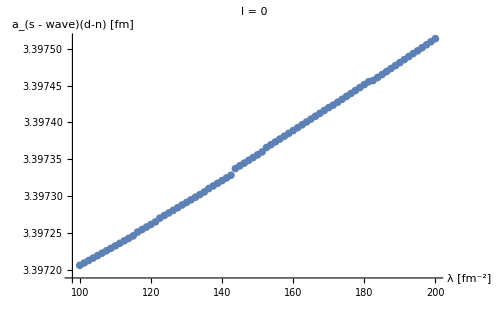

```mathematica
nGrid=300;
Lrel=0;
aOfa={};
rr=40;
α0=1.2;

λRange=Subdivide[100,200,80];


aS={};
SetSharedVariable[aS];

ParallelDo[
TanDelSwave=Chop[SolveSecular[rr,nGrid,k0FM,0,λ,-100 λ,0.0,α0,cfg,mh2]];
AppendTo[aS,{λ,-TanDelSwave/k0FM}];
,{λ,λRange}];

a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];

ListPlot[a0,AxesLabel->{"λ [fm^-2]","a_(s - wave)(d-n) [fm]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```